## Javier Salazar 1001144647

## Project 3.

1.   Assume that a department store at the border between State 1 and State 2 receives 4 calls  per hour.  Given that fact that 
      State 1 has twice as many people as State 2  analyze the marked Poisson Process N(t) during the hours of  4 PM - 9 PM.
(a)  Simulate a sample of  N(t) and mark each call as either type 1 or type 2  for the appropriate probability  p = P(1) 
      and 1-p = P(2).  Use ListPlot[ . ] to display the sample in three separate graphs as follows: 
      g1 ~  N1(t) = type 1 process marked  with point size .04,  g2 ~ N2 (t) = type 2 process marked with point size .02, 
      g3 ~ N(t) = N1(t) + N2(t) = combined process.
(b)  Simulate  N(t) = N1(t) + N2(t)  n = 100, 1000, 10000 times, find the corresponding sample average  and variance for  
      N(t), N1(t), N2(t)  (use Mean[ .] and Variance[ . ])  and compare with the corresponding exact values.

```mathematica
t=5;λ=4;s=0;A1={};A2={};n=0;
r=Random[ExponentialDistribution[λ]];type=RandomInteger[{1,3}]; s=s+r;
       While[s≤t,n=n+1;If[type==1 || type==3,AppendTo[A1,{s,n}],AppendTo[A2,{s,n}]];
                  r=Random[ExponentialDistribution[λ]];type=RandomInteger[{1,3}];
                  s=s+r]
```

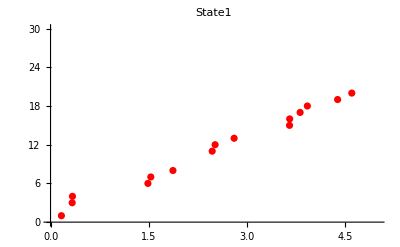

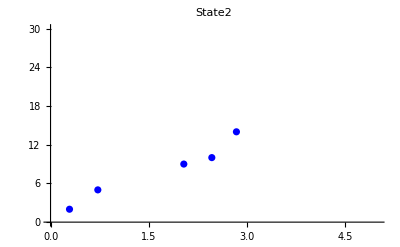

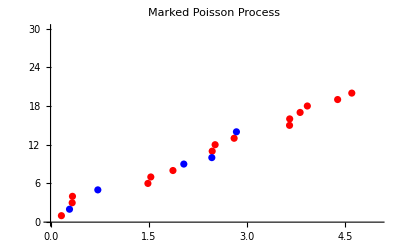

```mathematica
g1=ListPlot[A1,PlotStyle->Red,PlotStyle->PointSize[.04],PlotRange->{{0,5},{0,30}},PlotLabel->State1]
g2=ListPlot[A2,PlotStyle->Blue,PlotStyle->PointSize[.02],PlotRange->{{0,5},{0,30}},PlotLabel->State2]
Show[{g1,g2},PlotLabel->"Marked Poisson Process"]
```

```mathematica
Clear[a,s,t,r,λ,m1,n];  n=100;λ=4*2/3;t=5;m1={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m1,a],{n}]

Clear[a,s,t,r,λ,m2,n];  n=100;λ=4*1/3;t=5;m2={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m2,a],{n}]
Mean[m1]//N
Variance[m1]//N
Mean[m2]//N
Variance[m2]//N
Mean[m1]+Mean[m2]//N
Variance[m1]+Variance[m2]//N
```

12.92

14.3572

6.3

5.48485

19.22

19.842

```mathematica
Clear[a,s,t,r,λ,m1,n];  n=1000;λ=4*2/3;t=5;m1={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m1,a],{n}]

Clear[a,s,t,r,λ,m2,n];  n=1000;λ=4*1/3;t=5;m2={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m2,a],{n}]
Mean[m1]//N
Variance[m1]//N
Mean[m2]//N
Variance[m2]//N
Mean[m1]+Mean[m2]//N
Variance[m1]+Variance[m2]//N
```

13.554

14.4415

6.771

6.65521

20.325

21.0967

```mathematica
Clear[a,s,t,r,λ,m1,n];  n=10000;λ=4*2/3;t=5;m1={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m1,a],{n}]

Clear[a,s,t,r,λ,m2,n];  n=10000;λ=4*1/3;t=5;m2={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m2,a],{n}]
Mean[m1]//N
Variance[m1]//N
Mean[m2]//N
Variance[m2]//N
Mean[m1]+Mean[m2]//N
Variance[m1]+Variance[m2]//N
```

13.3325

13.5367

6.6435

6.61207

19.976

20.1488

```mathematica
(*The true m1 is 13.33, true m2 is 6.67, and the mean of m1 + m2 is 20. Increasing sample size results in a convergent mean)
```

2.  Each cereal box contains a mascot from the set of  5 different kinds. Suppose a buyer comes to the store according 
     to Poisson process with the rate of one purchase per week.  Let N = the minimum number the required trips to the 
     store in order to complete the five different mascots collection (Coupon Collecting Problem). 
    (a)  Simulate 3 samples of  {x_1, , ... ,x_N} where x_i ∈{1, 2, 3, 4, 5},  x_N is the mascot completing the collection
           and  N = last purchase.
    (b)  Simulate n =1000, 10000, 100000 samples of  N, find  the sample average and compare with the exact value EN.

```mathematica
Clear[Num,Sample,outcome]
(Num=0;
Sample={};l={};
Label[start];
m=l;
outcome=RandomInteger[{1,5}];
AppendTo[Sample,outcome];
Num=Num+1;l=m∪{outcome};
If[l≠{1,2,3,4,5},Goto[start]])
Sample
```

{3,2,4,5,1}

```mathematica
Clear[Num,Sample,outcome]
(Num=0;
Sample={};l={};
Label[start];
m=l;
outcome=RandomInteger[{1,5}];
AppendTo[Sample,outcome];
Num=Num+1;l=m∪{outcome};
If[l≠{1,2,3,4,5},Goto[start]])
Sample
```

{5,3,1,3,4,3,1,4,5,3,2}

```mathematica
Clear[Num,Sample,outcome]
(Num=0;
Sample={};l={};
Label[start];
m=l;
outcome=RandomInteger[{1,5}];
AppendTo[Sample,outcome];
Num=Num+1;l=m∪{outcome};
If[l≠{1,2,3,4,5},Goto[start]])
Sample
```

{3,3,5,3,2,1,5,3,4}

```mathematica
average[n_]:=(NumTotal=0;Do[Num=0;l={};Label[start];m=l;outcome=RandomInteger[{1,5}];Num=Num+1;l=m∪{outcome};If[l≠{1,2,3,4,5},Goto[start]];NumTotal=NumTotal+Num,{n}];N[NumTotal/n])
```

```mathematica
Clear[t]
avg=0;
exact:=∫_0^∞ (1-(1-ⅇ^(-t/5))^5)ⅆt (*Alternatively, exact = 1 + 5/4 + 5/3 + 5/2 + 5*)
Print["The exact value is ", exact//N]
n={1000,10000,100000};
For[i=1,i<4,i++,avg=average[n[[i]]]; Print["For a sample size of n = ", n[[i]], ", the sample average is ", average[n[[i]]], " with an absolute relative error of ", Abs[(exact-avg)/exact]*100, "%" ]]
```

The exact value is 11.4167

For a sample size of n = 1000, the sample average is 11.405 with an absolute relative error of 1.69635%

For a sample size of n = 10000, the sample average is 11.5131 with an absolute relative error of 0.253723%

For a sample size of n = 100000, the sample average is 11.4329 with an absolute relative error of 0.127153%

3.   Let λ = 2, t = 5.  First simulate N according to Poisson random variable with parameter λt.  For this N 
     simulate uniform random variables U_1,U_2, ..., U_N  from [0, t] and re-order them from smallest to largest  OverHat[U_1]≤...≤ OverHat[U_N].
     The ordered sample (OverHat[U_1],OverHat[U_2],...,OverHat[U_N]) = (S_1, S_2,...,S_N) are the arrival times of the Poisson Process N(t). This is an
     alternative way of  simulating Poisson Process without using exponentially distributed interarrival times.  
     Graph a sample of  N(u), 0 ≤ u ≤ t.

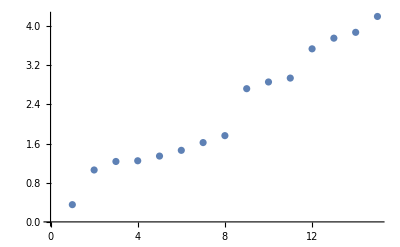

```mathematica
n=RandomVariate[PoissonDistribution[2*5]];
A=Sort[RandomVariate[UniformDistribution[{0,5}],{n}]];
ListPlot[A]
```

4.  Consider the Shock Model  A(t) = ∑_(i=i)^(N(t)) A_i e^(-α(t-S_i)) for α = 1/2, λ = 3, t =10, where N(t) is Poisson  ~ λ,  
     the amplitude of  i.i.d.  A_i ~ A has a uniform distribution U[1, 5], and S_iis the arrival time of the i-th shock for N(t). 
     Simulate  A(t)  n = 1000 times. Find the sample average and compare with exact value EA(t) = (λ E[A])/α(1-e^(-α t)).  
     Graph a sample of A(u), 0 ≤ u ≤ t.

```mathematica
Clear[n,A,s,shockTotal,list];
exactvalue:=3*3*2*(1-Exp[-.5*10])
list={};
For[j=1,j≤1000,j++,
n=RandomVariate[PoissonDistribution[3*10]];
A=RandomVariate[UniformDistribution[{1,5}],{n}];
s=Sort[Table[RandomReal[{0,10}],{n}]];
shockTotal:=Sum[A[[i]]*Exp[-0.5*(10-s[[i]])],{i,1,n}];
AppendTo[list,shockTotal];]
Print["The exact value is ", exactvalue]
Print["For a sample size of n = ", 1000, ", the sample mean is ", Mean[list], " with an absolute relative error of ", Abs[(exact-Mean[list])/exactvalue]*100, "%" ]
```

The exact value is 17.8787

For a sample size of n = 1000, the sample mean is 17.8886 with an absolute relative error of 36.1993%

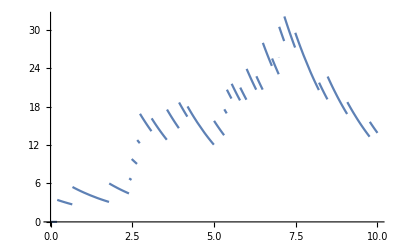

```mathematica
Clear[n,A,s,shockTotal,list];
n=RandomVariate[PoissonDistribution[3*10]];
A=RandomVariate[UniformDistribution[{1,5}],{n}];
s=Sort[Table[RandomReal[{0,10}],{n}]];
shockTotal[u_]:=Sum[A[[i]]*Exp[-0.5*(u-s[[i]])]*UnitStep[u-s[[i]]],{i,1,n}];
Plot[shockTotal[u],{u,0,10}]
```

5.  Consider a compound Poisson Process  X(t) = ∑_(i=1)^(N(t)) Y_i, where  N(t) ~ Poisson with  λ = 10/hour, t = 12  and 
     Y_i~ Y = Binomial  B(m,p) with p = 1/2,  m = 100.  By interpreting  N(t)  as the number of customers visiting a store 
     between  9AM - 9PM and each customer spending  $Y,   X(t) is the daily revenue for the store.  Simulate  X(t)
     n = 1000 times,  find the sample average and variance and compare with exact values EX(t) and VarX(t).  
     Graph a sample of  X(u) ,  0 ≤ u ≤ t.

```mathematica
Clear[n,A,s,compound,list];
list={};
exactmean:=6000 (*Mean of binomial is mp = 100*.5 = 50. And 50*120 = 6000*)
exactvariance:=303000 (*Mean = 100*.5*.5+50^2 = 25+2500 = 2525. And 2525*120 = 303000*)
For[j=1,j≤1000,j++,
n=RandomVariate[PoissonDistribution[10*12]];
Y=RandomVariate[BinomialDistribution[100,0.5],{n}];
s=Sort[Table[RandomReal[{0,12}],{n}]];
compound:=Sum[Y[[i]],{i,1,n}];
AppendTo[list,compound];]
Print["The exact mean is ", exactmean, " and the exact variance is ", exactvariance]
Print["For a sample size of n = ", 1000, ", the sample mean is ", Mean[list]//N, " with an absolute relative error of ", Abs[(exactmean-Mean[list])/exactmean]*100//N, "%" , " and sample variance is ", Variance[list]//N, " with an absolute relative error of ", Abs[(exactvariance-Variance[list])/exactvariance]*100//N, "%"]
```

The exact mean is 6000 and the exact variance is 303000

For a sample size of n = 1000, the sample mean is 5995.75 with an absolute relative error of 0.0708667% and sample variance is 309346. with an absolute relative error of 2.09426%

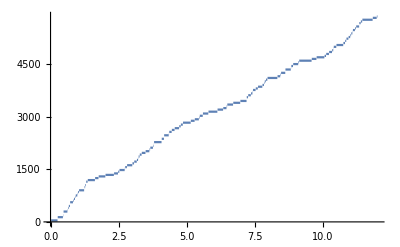

```mathematica
Clear[n,A,s,compound,list];
n=RandomVariate[PoissonDistribution[10*12]];
Y=RandomVariate[BinomialDistribution[100,0.5],{n}];
s=Sort[Table[RandomReal[{0,12}],{n}]];
compound[u_]:=Sum[Y[[i]]*UnitStep[u-s[[i]]],{i,1,n}];
Plot[compound[u],{u,0,12}]
```